# 10. Householder QR

```mathematica
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\Numerical-Linear-Algebra"]
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk01.mtx.gz"];
Export["bcsstk01.mtx", A]
```

C:\Users\AllanStruthers\Desktop\Numerical-Linear-Algebra

bcsstk01.mtx

## Householder Reflections

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}

## Householder QR

### Householder QR: Script Version 1

Here is a manual reduction of a Tall Skinny matrix A to upper triangular using Householder reflections. We are writing over the top of A to save space.  The fancy word for this is an “in-place” computation.

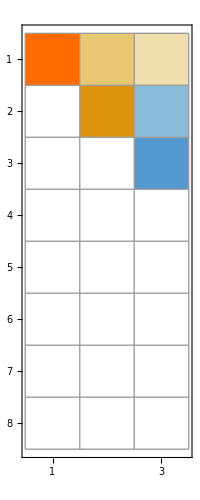

```mathematica
{m,n}={8,3};
A0=A=RandomReal[{-1,1},{m,n}];
a1=A⟦1;;-1,1⟧;
A⟦1;;-1,1⟧=HouseActionVec[A⟦1;;-1,1⟧,a1];
A⟦1;;-1,2⟧=HouseActionVec[A⟦1;;-1,2⟧,a1];
A⟦1;;-1,3⟧=HouseActionVec[A⟦1;;-1,3⟧,a1];
MatrixPlot[Chop[A],Mesh->All];
a2=A⟦2;;-1,2⟧;
A⟦2;;-1,2⟧=HouseActionVec[A⟦2;;-1,2⟧,a2];
A⟦2;;-1,3⟧=HouseActionVec[A⟦2;;-1,3⟧,a2];
MatrixPlot[Chop[A],Mesh->All];
a3=A⟦3;;-1,3⟧;
A⟦3;;-1,3⟧=HouseActionVec[A⟦3;;-1,3⟧,a3];
MatrixPlot[Chop[A],Mesh->All];
```

We have worked out what the QR algorithm (at least for R) is!

```mathematica
R=QRDecomposition[A0]⟦2⟧;
Chop[{A⟦1;;n⟧,R}]
```

{{{2.38596,0.460477,0.243277},{0,1.21882,-0.601005},{0,0,-1.01722}},{{2.38596,0.460477,0.243277},{0,1.21882,-0.601005},{0,0,-1.01722}}}

Notes:

We should do the columns together.

We do not have Q because we did not save it!  It is not a good idea to compute it at the end as Q=A.R^-1

Performant library code saves the Householder vectors (on top of the newly created zeros) and only builds an explicit Q matrix if needed.

### Householder QR: Script Version 2

Here is a less-manual script reducing a Tall Skinny matrix A to upper triangular using Householder reflections again overwriting A.

12

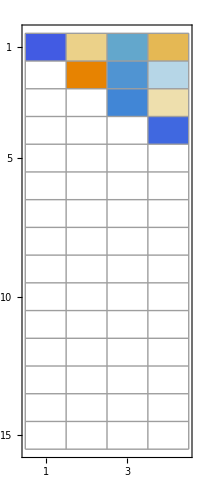

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}];
Do[
v=HouseVec[A⟦i;;-1,i⟧];
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n}]
{Q,R} =QRDecomposition[A];
TabView[Map[MatrixForm,Chop[{R,A⟦1;;n,1;;n⟧}]]]
MatrixPlot[Chop[A],Mesh->All]
```

We are going to save the Householder vectors (so that we can build Q) in the next version!

### Householder QR: Script Version 3

Here is a less-manual script reducing a Tall Skinny matrix A to upper triangular overwriting A and saving the Householder vectors.

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}]; V=0.0*A;
Do[
v=HouseVec[A⟦i;;-1,i⟧]; V⟦i;;-1,i⟧=v;
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n}]
{Q,R} =QRDecomposition[A];
TabView[Map[MatrixPlot[#, Mesh->All]&,{Chop[A],V}]]
```

12

Note: Performant code stuffs the reduced A and Householder vectors V together in a single rectangular matrix.

Yes they overlap! You either need a little extra storage vector (for the diagonals) or you need to remember that since the Householder vectors are unit vectors they have one less Degree of Freedom.

Next we are going to work out how to build the Householder Q from all the Householder vectors in V.

### Householder QR: Function

Here is a function reducing a Tall Skinny matrix A to upper triangular which overwrites A and returns the Householder vectors.

Here is an in-place Mathematica code.  HoldFirst prevents evaluation of the first argument A! As a result, the name (memory address) of the matrix A is handed to the function rather than making a copy of the matrix A and handing the copy off to the function!  The specified operations are done on the “original” matrix and we do not need to return anything! Since matrices can be (in the real world almost always are) very large this is much more efficient.

```mathematica
SetAttributes[MyQR,HoldFirst]
MyQR[A_]:= Module[{m,n,v,V},
{m,n}=Dimensions[A];
V=ConstantArray[0,{m,n}];
(* Householder Reduction from Script Version 3 *)
Do[
v=HouseVec[A⟦i;;-1,i⟧]; V⟦i;;-1,i⟧=v;
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n}];
(* Returns Householder vectors in V *)
V
]
```

As always TEST as best you can!  To test properly we need the Q!

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}]; V=0.0*A;
V=MyQR[A];
R=Chop[A⟦1;;n,1;;n⟧]
```

{{-2.51767,-0.532725,0.29488,0.079178},{0,-2.11629,0.144502,-0.54592},{0,0,-2.2619,0.843195},{0,0,0,-1.49213}}

Next we are going to work out how to build the Householder Q from all the Householder vectors in V.

## Householder Q

### Building Q from V Plan 1

We reduce the tall-skinny m×n matrix A_0 with a sequence of Householder reflectors that created zeros in the lower triangle of A_0

The first reflector H_1=I-v_1⊗v_1is m×m.  After the first step we have A_1=H_1.A_0 with a reduced first column.

The second one I-v_2⊗v_2is (m-1)×(m-1) which acts only on the lower (m-1)×n portion of A_1to give A_2.

Embedding it in the m×m reflector H_2=(1 | 0
0 | Id-v_2⊗v_2) lets us write A_2=H_2.A_1=H_2.H_1.A_0.

The third one I-v_3⊗v_3is (m-2)×(m-2) which acts only on the lower (m-2)×n portion of A_2 to give A_3.

Embedding it in the m×m reflector H_3=((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | Id-v_3⊗v_3) lets us write A_3=H_3.H_2.H_1.A_0.

When we are done we have (R
0)=A_n=H_n.H_(n-1).(…H)_2.H_1.A_0

By construction the product  H=H_n.H_(n-1).(…H)_2.H_1satisfies H.A_0=(R
0)

Since Hᵀ.H=Id we have A_0=Hᵀ.(R
0)

If Qᵀ is the first n rows of H i.e Qᵀ=H⟦1; ;n,1; ;m⟧  then A_0=Q.R

There are actually two things we might be interested in

The entire square matrix Q_big=Hᵀ=(H_n.H_(n-1).(…H)_2.H_1)ᵀ=H_1.H_2....H_n

The tall skinny m×n matrix Q from the QR decomposition Q=Q_big⟦1; ;m,1; ;n⟧.

### Householder H: Function

Here is a function reducing a Tall Skinny matrix A to upper triangular which overwrites A and returns the entire Householder H.

```mathematica
SetAttributes[QRH,HoldFirst]
QRH[A_]:= Module[{m,n,v,H},
{m,n}=Dimensions[A];
H=IdentityMatrix[m];
(* Householder Reduction from Script Version 3 *)
Do[
v=HouseVec[A⟦i;;-1,i⟧]; 
(* Reduces A *)
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}];
(* Updates H with v. Note it needs to do all the columns *)
Do[
H⟦i;;-1,j⟧=H⟦i;;-1,j⟧-2 v (v.H⟦i;;-1,j⟧),
{j,1,m}],
{i,1,n}];
(* Returns Accumulated Householder H *)
H
]
```

As always TEST!  T

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}]; V=0.0*A;
H=QRH[A];QBig=Hᵀ; R=A⟦1;;n,1;;n⟧; Q=QBig⟦All,1;;n⟧;
Map[Norm,{Hᵀ.H-IdentityMatrix[m],A-H.A0,A0-QBig.A, A0-Q.R}]
Map[Norm,{Hᵀ.H-IdentityMatrix[m],QBigᵀ.QBig -IdentityMatrix[m],Qᵀ.Q - IdentityMatrix[n]}]
```

{1.22471×10^-15,1.18244×10^-15,2.71471×10^-15,2.60322×10^-15}

{1.22471×10^-15,1.25208×10^-15,6.17161×10^-16}

This is very inefficient for tall-skinny matrices if you only need the tall-skinny Q.

### Building Q from V Plan 2

We reduce the tall-skinny m×n matrix A_0 with a sequence of Householder reflectors that created zeros in the lower triangle of A_0

H=H_n.H_(n-1).(…H)_2.H_1 satisfies H.A_0=(R
0)  where

H_1=I-v_1⊗v_1 and more generally

H_i=H_3=(I_(i-1) | 0
0 | I_i-v_i⊗v_i)

QBig=Hᵀ=H_1.H_2(…H)_n and the first n columns of QBig which gives the QR decomposition

The key is to remember that

B.e_i gives column i  of any matrix B

If I compute H_1. H_2 (…H)_n.e_1 I get the first column of QBig.

If I compute H_1. H_2 (…H)_n.(I_(n×n)
0_((m-n)×n)) I get the first n columns of QBig otherwise known as Q

I am going to build a function that computes H.X where H is specified by the tall skinny matrix of Householder Vs.

It looks very similar to the H bit in plan2 but the loop runs backwards.

### Building Q from V: Function

As before we update X in place.  I got fancy and tested if the dimensions matched!

```mathematica
SetAttributes[ApplyHouseholderV,HoldFirst]
ApplyHouseholderV[X_,V_]:= Module[{m,n,mr,r},
{m,n}=Dimensions[V];
{mr,r}=Dimensions[X];
If[mr≠m,Return["ApplyHousholderV: Dimension mismatch!"]];
Do[
v=V⟦All,j⟧;
Do[X⟦All,i⟧=X⟦All,i⟧-2 v (v.X⟦All,i⟧),
{i,1,r}],
{j,n,1,-1}]
]
```

As always test! First the intended use case!

```mathematica
{m,n}={12,4};
A=A0=RandomReal[{-1,1},{m,n}];
V=MyQR[A0]; R=A0⟦1;;n,1;;n⟧;
Q=0*V;Q⟦1;;n,1;;n⟧=IdentityMatrix[n];
ApplyHouseholderV[Q,V]
MatrixPlot[Q];
Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R}]
```

{1.50099×10^-15,3.87263×10^-15}

Now we get to test the error message as well.

```mathematica
{m,n}={12,4};{mr,nr}={11,4};
V =RandomReal[{-1,1},{m,n}]; 
X =RandomReal[{-1,1},{mr,nr}];
ApplyHouseholderV[X,V]
```

ApplyHousholderV: Dimension mismatch!

## Bonus: Fast Orthogonal Vectors

Suppose I would like r vectors (r is very small compared to m and small compared to n) that are orthogonal to the column space of tall-skinny m×n matrix A. We will see places later where this is not a weird thing to want.

Compute the Householder reduction of A and save the Householder vectors V.

Applying the Householder vectors V to any set of vectors X=(0_(n×r)
Y_((m-n)×r)) to compute H.X gives a set of r vectors orthogonal to the orthogonal basis Q for the column space of A.

Even better, if Y is orthogonal then so is H.X  and as a result [Q,X] is orthogonal!

```mathematica
{m,n,r}={12,4,3};
A=RandomReal[{-1,1},{m,n}];
V=MyQR[A]; VOld=V;
Q=0*V;Q⟦1;;n,1;;n⟧=IdentityMatrix[n];
ApplyHouseholderV[Q,V];
Y=QRDecomposition[RandomReal[{-1,1},{m-n,r}]]⟦1⟧ᵀ;
X=ArrayFlatten[({{ConstantArray[0,{n,r}]}, {Y}})];
ApplyHouseholderV[X,V];
{i,j}={1,1};
QX=ArrayFlatten[{{Q,X}}];
MatrixPlot[QX,PlotLabel->Norm[QXᵀ.QX - IdentityMatrix[n+r]],
PlotLegends->Automatic]
```

-Graphics-